```mathematica
NA = 6.0221367 10^23;
Dtot=10^-12;
kd=10^3;
sigma=1 10^-8;
kf=10 * sigma * Dtot;
kD=4*Pi*sigma*Dtot;
h=(1+kf/kD)*Sqrt[Dtot]/sigma;
a=kd*Sqrt[Dtot]/sigma;
r0=sigma;
tau = sigma^2 / Dtot;
t= tau 10^-2;
maxr = 4.5 Sqrt[ 6 Dtot t]+sigma;
```

```mathematica
ciccio=N[Solve[{x+y+z==h, x*y+y*z+x*z==kd,x*y*z==a},{x,y,z}]];
alpha=ciccio[[1,1,2]];
beta = ciccio[[1,2,2]];
gamma=ciccio[[1,3,2]];
```

```mathematica
W[x_,y_]:=Exp[2*x*y+y^2]*Erfc[x+y];
frac[x_,y_,z_]:=(x*(z+x)*(x+y))/((z-x)*(x-y));
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[Dtot]);
term1[r_]:=1/Sqrt[4*Pi*t]*(Exp[-(r-r0)^2/(4*Dtot*t)]+Exp[-(r+r0-2*sigma)^2/(4*Dtot*t)]);
term2[r_]:=frac[alpha,beta,gamma]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),alpha*Sqrt[t]];
term3[r_]:=frac[beta,gamma,alpha]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),beta*Sqrt[t]];
term4[r_]:=frac[gamma,alpha,beta]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),gamma*Sqrt[t]];
```

```mathematica
f[r_]:=4*Pi*r^2*Re[coeff[r]*(term1[r]+term2[r]+term3[r]+term4[r])]
```

c = N[Integrate[f[r], {r, 1, Infinity}]]

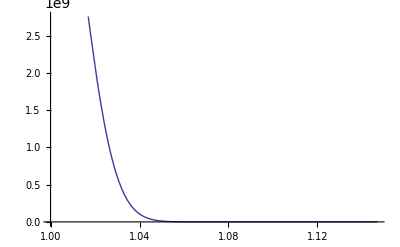

```mathematica
Plot[f[r], {r,sigma,maxr}]
```

```mathematica
out=Table[{r,f[r]},{r,sigma,maxr,(maxr - sigma) / 100}] // N
```

{{1.×10^-8,5.4659×10^9},{1.00147×10^-8,5.45794×10^9},{1.00294×10^-8,5.38985×10^9},{1.00441×10^-8,5.2641×10^9},{1.00588×10^-8,5.08496×10^9},{1.00735×10^-8,4.85824×10^9},{1.00882×10^-8,4.59102×10^9},{1.01029×10^-8,4.2913×10^9},{1.01176×10^-8,3.96758×10^9},{1.01323×10^-8,3.62848×10^9},{1.0147×10^-8,3.28241×10^9},{1.01617×10^-8,2.9372×10^9},{1.01764×10^-8,2.59987×10^9},{1.01911×10^-8,2.27642×10^9},{1.02058×10^-8,1.97168×10^9},{1.02205×10^-8,1.6893×10^9},{1.02352×10^-8,1.43175×10^9},{1.02498×10^-8,1.20038×10^9},{1.02645×10^-8,9.95547×10^8},{1.02792×10^-8,8.1677×10^8},{1.02939×10^-8,6.62878×10^8},{1.03086×10^-8,5.32188×10^8},{1.03233×10^-8,4.22663×10^8},{1.0338×10^-8,3.32064×10^8},{1.03527×10^-8,2.58077×10^8},{1.03674×10^-8,1.98417×10^8},{1.03821×10^-8,1.50907×10^8},{1.03968×10^-8,1.13538×10^8},{1.04115×10^-8,8.45034×10^7},{1.04262×10^-8,6.22173×10^7},{1.04409×10^-8,4.5316×10^7},{1.04556×10^-8,3.2651×10^7},{1.04703×10^-8,2.32726×10^7},{1.0485×10^-8,1.64096×10^7},{1.04997×10^-8,1.1446×10^7},{1.05144×10^-8,7.89801×10^6},{1.05291×10^-8,5.3912×10^6},{1.05438×10^-8,3.64049×10^6},{1.05585×10^-8,2.43186×10^6},{1.05732×10^-8,1.60703×10^6},{1.05879×10^-8,1.05055×10^6},{1.06026×10^-8,679381.},{1.06173×10^-8,434628.},{1.0632×10^-8,275061.},{1.06467×10^-8,172205.},{1.06614×10^-8,106652.},{1.06761×10^-8,65343.4},{1.06908×10^-8,39604.1},{1.07055×10^-8,23745.7},{1.07201×10^-8,14084.4},{1.07348×10^-8,8264.16},{1.07495×10^-8,4796.96},{1.07642×10^-8,2754.49},{1.07789×10^-8,1564.67},{1.07936×10^-8,879.253},{1.08083×10^-8,488.778},{1.0823×10^-8,268.793},{1.08377×10^-8,146.228},{1.08524×10^-8,78.6959},{1.08671×10^-8,41.8969},{1.08818×10^-8,22.0657},{1.08965×10^-8,11.4964},{1.09112×10^-8,5.92539},{1.09259×10^-8,3.02119},{1.09406×10^-8,1.52387},{1.09553×10^-8,0.760369},{1.097×10^-8,0.375327},{1.09847×10^-8,0.183275},{1.09994×10^-8,0.0885331},{1.10141×10^-8,0.0423073},{1.10288×10^-8,0.0200002},{1.10435×10^-8,0.00935322},{1.10582×10^-8,0.00432709},{1.10729×10^-8,0.00198034},{1.10876×10^-8,0.000896584},{1.11023×10^-8,0.000401561},{1.1117×10^-8,0.000177918},{1.11317×10^-8,0.0000779824},{1.11464×10^-8,0.0000338129},{1.11611×10^-8,0.0000145036},{1.11758×10^-8,6.1543×10^-6},{1.11905×10^-8,2.58339×10^-6},{1.12051×10^-8,1.07277×10^-6},{1.12198×10^-8,4.40693×10^-7},{1.12345×10^-8,1.79091×10^-7},{1.12492×10^-8,7.19975×10^-8},{1.12639×10^-8,2.86333×10^-8},{1.12786×10^-8,1.1265×10^-8},{1.12933×10^-8,4.38433×10^-9},{1.1308×10^-8,1.68804×10^-9},{1.13227×10^-8,6.4294×10^-10},{1.13374×10^-8,2.42252×10^-10},{1.13521×10^-8,9.02968×10^-11},{1.13668×10^-8,3.32955×10^-11},{1.13815×10^-8,1.21453×10^-11},{1.13962×10^-8,4.38267×10^-12},{1.14109×10^-8,1.56451×10^-12},{1.14256×10^-8,5.52494×10^-13},{1.14403×10^-8,1.93012×10^-13},{1.1455×10^-8,6.67037×10^-14},{1.14697×10^-8,2.28047×10^-14}}

```mathematica
Export["p_rev.-2.tsv",out]
```

p_rev.-4.tsv